```mathematica
ClearAll["Global`*"];
```

```mathematica
a:=1;σ:=2; n=500;γ=0.75;
D1=LogNormalDistribution[a,σ];
PDF[D1,x]
```

Piecewise[{{(ⅇ^(-1/8 (-1+Log[x])^2))/(2 √(2 π) x), x>0}, {0, True}}]

```mathematica
N[Mean[D1]]
```

20.0855

```mathematica
N[Variance[D1]]
```

21623.

```mathematica
X=RandomVariate[D1,n];
Y=Sort[X]
```

{0.00167808,0.00799456,0.011786,0.0122218,0.0165515,0.023701,0.0243741,0.0278845,0.0306351,0.0339653,0.0388062,0.0398255,0.0412574,0.0419619,0.043734,0.0493089,0.0524139,0.055174,0.071347,0.0715965,0.0744065,0.0753953,0.0770986,0.0783243,0.0804072,0.0829589,0.0899773,0.0957915,0.098302,0.100578,0.102631,0.108206,0.108551,0.112056,0.115338,0.117742,0.118468,0.123046,0.125878,0.127332,0.130501,0.131253,0.131272,0.131871,0.134225,0.134468,0.134474,0.136539,0.146118,0.148675,0.151007,0.153872,0.166312,0.170614,0.177313,0.181764,0.188861,0.208636,0.208659,0.213551,0.213997,0.216315,0.223369,0.226557,0.2307,0.232505,0.234803,0.236919,0.244027,0.249152,0.258502,0.261904,0.272506,0.27293,0.27334,0.273531,0.273644,0.281147,0.281679,0.287789,0.288357,0.294823,0.29791,0.302223,0.307532,0.323812,0.32698,0.330419,0.330606,0.335412,0.338025,0.344552,0.352191,0.356185,0.364131,0.365192,0.366674,0.370821,0.378858,0.385582,0.393371,0.395107,0.400854,0.408945,0.426292,0.430962,0.432409,0.436775,0.442382,0.445312,0.451143,0.453448,0.456875,0.462338,0.464285,0.479329,0.482334,0.482862,0.490986,0.496564,0.500349,0.52504,0.547967,0.55725,0.559698,0.566538,0.574626,0.591927,0.598228,0.621145,0.621182,0.62352,0.62449,0.639144,0.643994,0.648865,0.662271,0.663717,0.666693,0.668423,0.67491,0.686257,0.689303,0.694592,0.694677,0.702557,0.707913,0.718127,0.731442,0.771001,0.777268,0.782611,0.791318,0.799564,0.805292,0.845949,0.853808,0.863222,0.873814,0.884706,0.886372,0.890485,0.893244,0.902692,0.924197,0.933425,0.942299,0.946733,0.953556,0.959539,0.982047,1.00248,1.00422,1.00886,1.0092,1.018,1.03011,1.03543,1.03688,1.04348,1.04818,1.04842,1.05706,1.06182,1.07885,1.09093,1.09518,1.1119,1.1166,1.14679,1.1586,1.21226,1.22088,1.22721,1.23575,1.23582,1.27219,1.29494,1.30495,1.31828,1.32123,1.32927,1.34523,1.34874,1.35536,1.35569,1.35691,1.36473,1.37672,1.37882,1.39481,1.41876,1.44522,1.47007,1.47345,1.48047,1.54817,1.56391,1.56624,1.57049,1.57672,1.58871,1.59567,1.63055,1.75666,1.77577,1.78448,1.8458,1.86046,1.86504,1.88786,1.94929,1.98043,1.99485,2.00423,2.10054,2.1386,2.18372,2.19202,2.19705,2.28126,2.34638,2.3695,2.41543,2.41693,2.43358,2.43965,2.45104,2.45653,2.45808,2.47965,2.50428,2.51389,2.57295,2.59654,2.63389,2.64786,2.66669,2.66938,2.68977,2.69878,2.74761,2.77548,2.78533,2.78704,2.80445,2.87291,2.92443,2.93137,2.95954,3.22208,3.22213,3.22668,3.2335,3.31261,3.34932,3.40525,3.45532,3.48119,3.52122,3.57446,3.5891,3.60923,3.62974,3.65168,3.76943,3.7808,3.81971,3.83161,3.83318,3.89465,3.89965,3.90842,3.96368,4.0443,4.05898,4.107,4.16576,4.17118,4.34255,4.42677,4.44566,4.48689,4.4928,4.58887,4.61839,4.69452,4.78662,4.91434,4.93943,4.96916,5.17464,5.26235,5.26398,5.26811,5.28285,5.37069,5.3855,5.40494,5.43094,5.4817,5.54056,5.58905,5.59617,5.76975,5.77838,5.8287,5.84572,5.86413,5.99629,6.02637,6.03822,6.07537,6.18392,6.20411,6.24133,6.31574,6.43781,6.59055,6.65867,6.76159,6.90859,7.19645,7.24962,7.2516,7.26107,7.46649,7.5871,7.65587,7.68919,7.91576,7.99451,8.017,8.17837,8.18438,8.21534,8.32261,8.46464,8.53142,8.67715,8.86199,8.89667,8.92351,9.10245,9.11673,9.4748,9.53118,9.73995,9.79308,9.87703,9.8902,10.2003,10.244,10.2931,10.4323,10.5072,10.5271,10.6448,10.8637,11.1158,11.2513,11.2659,11.3368,11.5129,11.6438,11.7016,11.7928,11.8029,11.8643,11.9252,12.0976,12.1389,12.1726,12.2539,12.3237,12.3316,12.8975,12.9115,13.0152,13.0254,13.1848,13.6167,13.7067,13.758,13.8066,13.9643,14.0769,14.5292,15.4353,15.5631,15.5666,16.0292,16.1763,16.1916,16.5087,16.8771,18.2852,19.1943,19.2714,19.284,20.1667,20.509,20.8194,20.8739,21.128,21.1704,22.6319,23.1683,23.6435,23.7164,23.9535,23.9642,24.4015,24.4229,24.5211,24.567,24.9112,25.0389,25.3286,26.6697,27.57,27.7644,28.2699,28.5615,29.2511,29.6419,30.0255,30.0688,30.1431,30.3308,30.7142,31.9012,32.4766,32.5951,33.2449,34.3747,35.8999,37.3958,40.4782,40.807,41.994,43.0922,44.9078,45.164,46.7113,47.8135,47.9876,48.0975,48.4264,49.2213,49.6391,50.6049,50.7127,51.3453,51.4776,53.0352,53.6864,54.0953,56.4755,67.7686,71.4025,75.1471,76.5013,87.5451,91.1111,98.8554,103.245,103.982,108.236,113.641,115.658,128.971,161.787,318.569,319.508,366.058,405.266,618.939,630.291,986.409}

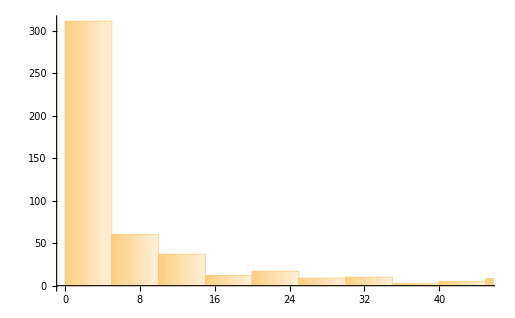

```mathematica
Histogram[X,ChartElementFunction->"FadingRectangle",AxesStyle->Thick,LabelStyle->Directive[15]]
```

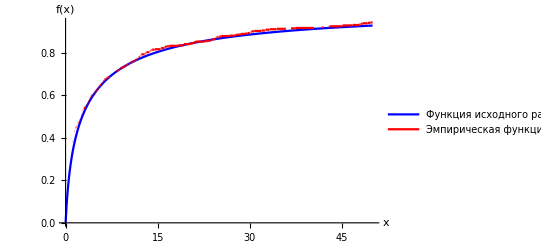

```mathematica
F[x_]:=CDF[EmpiricalDistribution[X],x];
Plot[{CDF[D1,x],F[x]},{x,0,50},PlotRange->All,AxesStyle->Thick,LabelStyle->Directive[20],PlotStyle->{Blue,Red},PlotLegends->{"Функция исходного распределения","Эмпирическая функция распределения"},AxesLabel->{"x","f(x)"}]
```

```mathematica
(*ВЫБОРОЧНОЕ МАТ ОЖИДАНИЕ И ДИСПЕРСИЯ*)
```

```mathematica
M=(∑_(i=1)^n X[[i]])/n
```

17.1444

```mathematica
S=(∑_(i=1)^n (X[[i]]-M)^2)/n
```

4697.16

```mathematica
(*КВАНТИЛИ*)
```

```mathematica
{g1,g2}=Quantile[GammaDistribution[n/2,8],{(1-γ)/2,(1+γ)/2}]
```

{1855.45,2146.28}

```mathematica
(*ОПТИМАЛЬНАЯ ОЦЕНКА*)
N[Gamma[n/2]/Gamma[(n+1)/2] √((∑_(i=1)^n (Log[X[[i]]]-a)^2)/8)]
```

1.035

```mathematica
(*ОЦЕНКА МАКСИМАЛЬНОГО ПРАВДОПОДОБИЯ (смещенная)*)
N[√((∑_(i=1)^n (Log[X[[i]]]-a)^2)/(4n))]
```

1.03448

```mathematica
(*ОЦЕНКА МЕТОДОМ МОМЕНТОВ*)
N[√((Log[M]-a)/2)]
```

0.959603

```mathematica
(*γ-ДОВЕРИТЕЛЬНЫЙ ИНТЕРВАЛ*)
```

```mathematica
N[√((∑_(i=1)^n (Log[X[[i]]]-a)^2)/g2)]
```

0.998608

```mathematica
N[√((∑_(i=1)^n (Log[X[[i]]]-a)^2)/g1)]
```

1.07402

```mathematica
(*ПРОВЕРКА ГИПОТЕЗЫ О ВИДЕ РАСПРЕДЕЛЕНИЯ*)
(*КРИТЕРИЙ КОЛМОГОРОВА*)
α=0.09;(*уровень значимости критерия*)
Dn=N[Max[Table[Abs[F[x]-CDF[D1,x]],{x,0,1000}]]]
```

0.0334625

```mathematica
k=1.24;(*квантиль распределения Колмогорова уровня 1-α*)
k/√n
```

0.0554545

```mathematica
Dn<k/√n
```

True

```mathematica
(*Cледовательно, по критерию Колмогорова, гипотеза о виде распределения не противоречит выборке*)
```

```mathematica
(*КРИТЕРИЙ ХИ-КВАДРАТ*)
ν=Last[HistogramList[Y,{{0,0.5,1,2,4,6,8,10,100,1000}},"Count"]]
```

{120,51,63,60,36,22,19,115,14}

```mathematica
p0={NIntegrate[PDF[D1,x],{x,0,0.5}],NIntegrate[PDF[D1,x],{x,0.5,1}],NIntegrate[PDF[D1,x],{x,1,2}],NIntegrate[PDF[D1,x],{x,2,4}],NIntegrate[PDF[D1,x],{x,4,6}],NIntegrate[PDF[D1,x],{x,6,8}],NIntegrate[PDF[D1,x],{x,8,10}],NIntegrate[PDF[D1,x],{x,10,100}],NIntegrate[PDF[D1,x],{x,100,1000}]}
```

{0.198616,0.109921,0.130493,0.137547,0.077325,0.0514021,0.037266,0.221702,0.0341577}

```mathematica
𝒳squareStat=N[Plus@@((ν-n p0)^2/(n p0))]
```

7.22721

```mathematica
Quantile[ChiSquareDistribution[Length[ν]-1],1-α]
```

13.6975

```mathematica
(*Cледовательно, по критерию хи-квадрат, гипотеза о виде распределения не противоречит выборке*)
```

```mathematica
ClearAll["Global`*"];
```

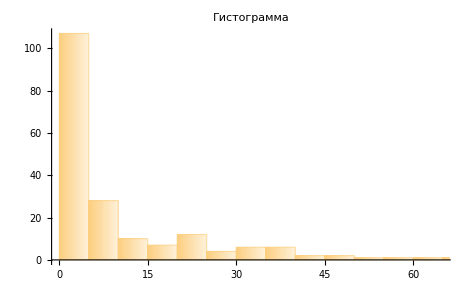

```mathematica
a:=1;σ:=2; n=200;γ=0.75;
D1=LogNormalDistribution[a,σ];
For[i=1,i≤10,i++,Subscript[X, i]=RandomVariate[D1,n];];Histogram[Subscript[X, 1],ChartElementFunction->"FadingRectangle",PlotLabel->Гистограмма ,AxesStyle->Thick,LabelStyle->Directive[15]]
```

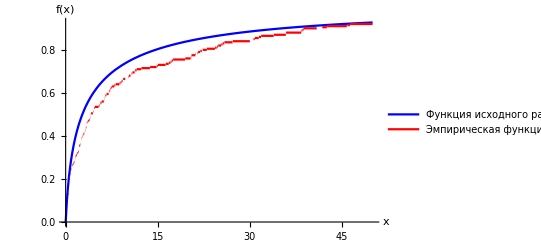

```mathematica
F[x_]:=CDF[EmpiricalDistribution[Subscript[X, 1]],x];
Plot[{CDF[D1,x],F[x]},{x,0,50},PlotRange->All,AxesStyle->Thick,LabelStyle->Directive[20],PlotStyle->{Blue,Red},PlotLegends->{"Функция исходного распределения","Эмпирическая функция распределения"},AxesLabel->{"x","f(x)"}]
```

```mathematica
{g1,g2}=Quantile[GammaDistribution[n/2,8],{(1-γ)/2,(1+γ)/2}]
```

{708.979,892.745}

```mathematica
gridLabel1={"X","Выборочное МО","Выборочная дисперсия","ММ","Оптимальная оценка","γ-доверительный интервал"};gridData1=Table[Table[{},{j,1,Length[gridLabel1]}],{i,1,10}];gridData1[[All,1]]=Table[Subscript["X", i],{i,1,10}];For[j=1,j≤10,j++,gridData1[[j,2]]=N[(∑_(i=1)^n Subscript[X, j][[i]])/n]];For[j=1,j≤10,j++,gridData1[[j,3]]=N[(∑_(i=1)^n (Subscript[X, j][[i]]-gridData1[[j,2]])^2)/n]];
For[j=1,j≤10,j++,gridData1[[j,4]]=N[√((Log[gridData1[[j,2]]]-a)/2)]];
For[j=1,j≤10,j++,gridData1[[j,5]]=N[Gamma[n/2]/Gamma[(n+1)/2] √((∑_(i=1)^n (Log[Subscript[X, j][[i]]]-a)^2)/8)]];
For[j=1,j≤10,j++,gridData1[[j,6]]=N[{√((∑_(i=1)^n (Log[Subscript[X, j][[i]]]-a)^2)/g2),√((∑_(i=1)^n (Log[Subscript[X, j][[i]]]-a)^2)/g1)}]];
θ1=gridData1[[All,4]];θ2=gridData1[[All,5]];
gridData1={gridLabel1}~Join~gridData1;
Grid[gridData1,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
```

X | Выборочное МО | Выборочная дисперсия | ММ | Оптимальная оценка | γ-доверительный интервал
X_1 | 19.1736 | 2171.57 | 0.988315 | 0.973927 | {0.920799,1.03326}
X_2 | 19.3796 | 8003.58 | 0.991016 | 0.91797 | {0.867895,0.973899}
X_3 | 14.9108 | 1544.8 | 0.92252 | 0.900369 | {0.851253,0.955225}
X_4 | 14.0839 | 1348.57 | 0.906927 | 0.876096 | {0.828304,0.929473}
X_5 | 17.5404 | 4427.79 | 0.965533 | 0.975099 | {0.921907,1.03451}
X_6 | 26.1446 | 9986.41 | 1.06387 | 1.00073 | {0.946139,1.0617}
X_7 | 14.2748 | 1582.26 | 0.91063 | 0.970243 | {0.917315,1.02936}
X_8 | 27.9433 | 23707.3 | 1.07939 | 1.04127 | {0.984468,1.10471}
X_9 | 24.0221 | 8843.66 | 1.04378 | 0.976095 | {0.922849,1.03557}
X_10 | 20.7646 | 3857.48 | 1.00828 | 0.989007 | {0.935056,1.04926}

```mathematica
(*ВЫБОРОЧНЫЕ ХАРАКТЕРИСТИКИ ОЦЕНОК*)
```

```mathematica
Mean[θ1]
```

0.988027

```mathematica
Mean[θ2]
```

0.96208

```mathematica
Variance[θ1]
```

0.00388809

```mathematica
Variance[θ2]
```

0.00246777